# MGDrivE: Software Paper Data Analysis

## Functions

```mathematica
SetDirectory[NotebookDirectory[]];
FixDataEntry[dataFileContent_]:=Append[#,#//Total]&/@(dataFileContent[[2;;All,2;;All]][[All,1;;(Length[dataFileContent[[1]]]-1)]])

Themes`AddThemeRules["MGDrivE_PopDyn",
DefaultPlotStyle->Thread@Directive[colorPalette,Thickness[.01]],
LabelStyle->15,
Frame->True,
FrameStyle->Directive[Thick,Gray],
FrameTicksStyle->Gray,
GridLines->Automatic,
PlotRange->{0,All},
ImageSize->Large,
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
Options[SplitPlotDynamics]={AspectRatios->{.75,.45},ImageSize->500};
SplitPlotDynamics[data_,ranges_,colorPalette_,OptionsPattern[]]:=Module[{plotRight,plotLeft,rangeA=ranges[[1]],rangeB=ranges[[2]]},
(**)
plotLeft=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[1]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeA,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Thick,Dashed},
{Thick,Thick}
},
FrameTicks->{{Automatic,None},{Range[0,rangeA[[2]]-1,100],None}},
FrameLabel->(Style[#,30]&/@{"Time","Population"})
];
plotRight=ListLinePlot[
data//Transpose,
AspectRatio->1/OptionValue[AspectRatios][[2]],
PlotTheme->"MGDrivE_PopDyn",
PlotStyle->colorPalette,
ImageSize->{Automatic,OptionValue[ImageSize]},
PlotRange->{rangeB,{0,Round[(Flatten[data]//Max)*.1]+(Flatten[data]//Max)}},
FrameStyle->{
{Dashed,Thick},
{Thick,Thick}
},
FrameTicks->{{None,All},{Range[0,rangeB[[2]]-1,500],None}},
FrameLabel->(Style[#,30,White]&/@{"Time","Population"})
];
Grid[{{plotLeft,plotRight}},Spacings->{0,0}]
]

ImportAndReshapeData[folderName_]:=Module[{fileNames,raw,data,dataTotal,maleFileNames,femaleFileNames,rawMale,rawFemale,dataMale,dataFemale,dataTotalMale,dataTotalFemale,genotypes},
fileNames={maleFileNames,femaleFileNames}=FileNames[folderName<>"/"<>#]&/@{"ADM*.csv","AF1_Aggregate*.csv"};
raw={rawMale,rawFemale}=Table[ParallelMap[Import[#]&,i],{i,fileNames}];
data={dataMale,dataFemale}=Table[#[[2;;All,3;;All]]&/@i,{i,raw}];
dataTotal={dataTotalMale,dataTotalFemale}=Table[Flatten/@Transpose[{Total/@#,#}]&/@i,{i,data}];
genotypes=Prepend[rawMale[[1,1,3;;All]],"Total"];
{genotypes,dataTotal}
]
CalculateQuartiles[genotypes_,data_]:=Module[{sexes,quartilesData,lowQuartile,medianQuartile,topQuartile},
sexes=2;
Table[
quartilesData=Table[Transpose[Quartiles/@Transpose[data[[j]][[All,All,i]]]],{i,1,genotypes//Length}];
{lowQuartile,medianQuartile,topQuartile}={quartilesData[[All,1]]//Transpose,quartilesData[[All,2]]//Transpose,quartilesData[[All,3]]//Transpose}
,{j,1,sexes}]
]
CreateColorSwatch[genotypes_,colorSchemeNumber_,{markerSize_,labelStyle_}]:=Module[{colorPalette,colorPairs,colorSwatch},
colorPalette=Prepend[ColorData[colorSchemeNumber,"ColorList"][[1;;(Length[genotypes]-1)]],Lighter[Black,.75]];
colorPairs=Transpose[{genotypes,colorPalette}];
colorSwatch=SwatchLegend[colorPairs[[All,2]],colorPairs[[All,1]],LegendMarkerSize->markerSize,LabelStyle->labelStyle,LegendLayout->{"Column",1}];
{colorPalette,colorSwatch}
]
ReshapeSexData[sexData_,quantile_]:=Module[{nodeDataAtTime,reshapedData},
reshapedData=Table[
Table[
nodeDataAtTime=Transpose[sexData][[node,All,time]];
Quantile[#,quantile]&/@Transpose[nodeDataAtTime]
,{time,1,sexData[[1,1]]//Length}]
,{node,1,sexData[[1]]//Length}];
reshapedData
]
ReshapeStochasticMultiNode[dataTotal_,quantile_]:=ParallelTable[ReshapeSexData[dataTotal[[All,i]],quantile],{i,1,2}]
```

```mathematica
SmoothHistogramPlot[sampledCoordinatesLayer_,{imageSize_,imagePadding_},plotRange_]:=SmoothHistogram[sampledCoordinatesLayer,
PlotStyle->Directive[{Thickness[.01],Opacity[.5]}],
ImageSize->imageSize,
PlotRange->{plotRange[[1]],plotRange[[2]]},
AspectRatio->.075,
Axes->False,
FrameStyle->Directive[Thick,Gray],
FrameTicks->{None,None},
Filling->Bottom,
Frame->True,
FrameLabel->None,
ImagePadding->imagePadding,
ImageSize->imageSize,
PlotTheme->"RandomPointsPlot"
]
ListPlotScatter[clusteredCoordinates_,{imageSize_,imagePadding_},plotRange_]:=
ListPlot[clusteredCoordinates,
FrameTicks->Automatic,
FrameStyle->Directive[Thick,Gray],
Axes->False,
GridLines->Automatic,
BaseStyle->15,
Frame->True,
AspectRatio->1,
LabelStyle->Directive[10],
FrameLabel->{{None,Rotate["y [meters]",180Degree]},{None,"x [meters]"}},
PlotRange->{plotRange[[1]],plotRange[[1]]},
PlotTheme->"RandomPointsPlot",
PlotStyle->Directive[{PointSize[.025],Red,Opacity[.35]}],
ImageSize->imageSize,
ImagePadding->imagePadding
]
CalculateEuclideanDistances[coordinates_]:=Table[N[EuclideanDistance[coordinates[[i]],#]]&/@coordinates,{i,1,coordinates//Length }]
```

## Single Node Deterministic (Single Run)

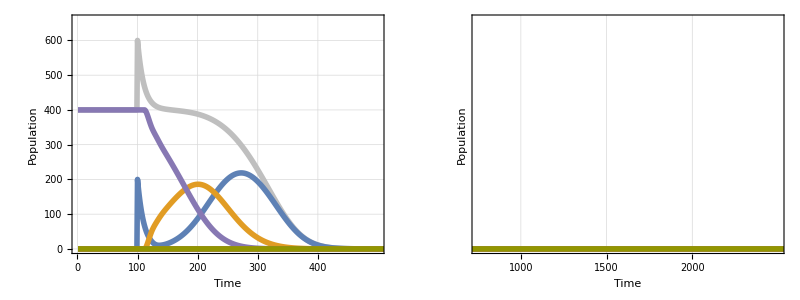
-Graphics- |  |  |  |

```mathematica
(*Load and reshape data*)
folder="OUT/SinglePop/CRISPR2R_SD";
{genotypes,dataTotal}=ImportAndReshapeData[folder];
{colorPalette,colorSwatch}=CreateColorSwatch[genotypes,97,{20,15}];
(*Plot results*)
plot=SplitPlotDynamics[dataTotal[[1,1]]+dataTotal[[2,1]],{{1,500},{750,2500}},colorPalette];
grid=Grid[{{plot,"","","",colorSwatch}}]
```

## Single Node Stochastic (Quartiles over Repetitions)

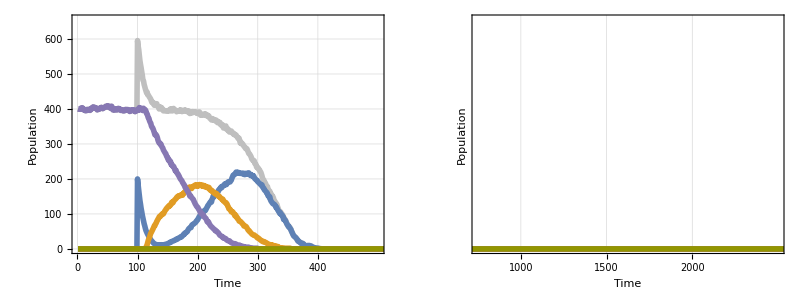
-Graphics- |  |  |  |

```mathematica
(*Load and reshape data*)
folder="OUT/SinglePop/CRISPR2R_SS";
{genotypes,dataTotal}=ImportAndReshapeData[folder];
(*{sex,repetitions,time}=dataTotal*)
quartiles={quartilesMale,quartilesFemale}=CalculateQuartiles[genotypes,dataTotal];
{colorPalette,colorSwatch}=CreateColorSwatch[genotypes,97,{20,15}];
(*Plot*)
quartile=2;
plot=SplitPlotDynamics[quartilesMale[[quartile]]+quartilesFemale[[quartile]],{{1,500},{750,2500}},colorPalette];
grid=Grid[{{plot,"","","",colorSwatch}}]
```

## Multi Node Deterministic (Single Run)

Load Data

```mathematica
(*Load and reshape data*)
baseFolder="OUT_ERACR_CPP/ERACRCornersDeterministic";
folder=FileNames["*",baseFolder]//DeleteCases[#,baseFolder<>"/.DS_Store"]&;
nodesData=Table[
{genotypes,dataTotal}=ImportAndReshapeData[folder[[i]]];
dataTotal
,{i,1,folder//Length}];
{colorPalette,colorSwatch}=CreateColorSwatch[genotypes,97,{20,15}];
```

Explore a Single Node

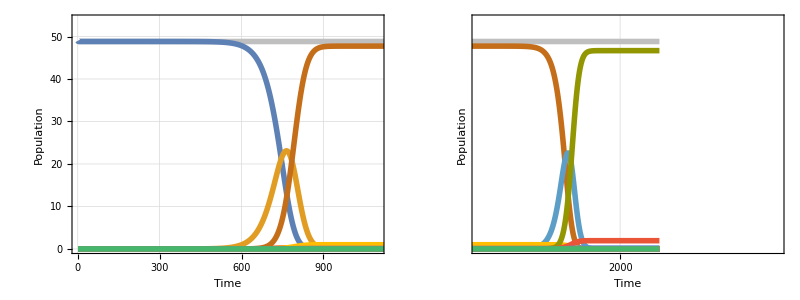
-Graphics- |  |  |  |

```mathematica
{repetition,node}={1,40};
{male,female}={1,2};
totalPopulation=nodesData[[repetition,male,node]]+nodesData[[repetition,female,node]];
(*Plot results*)
plot=SplitPlotDynamics[totalPopulation,{{1,1100},{1100,3000}},colorPalette];
grid=Grid[{{plot,"","","",colorSwatch}}]
```

Explore the Network

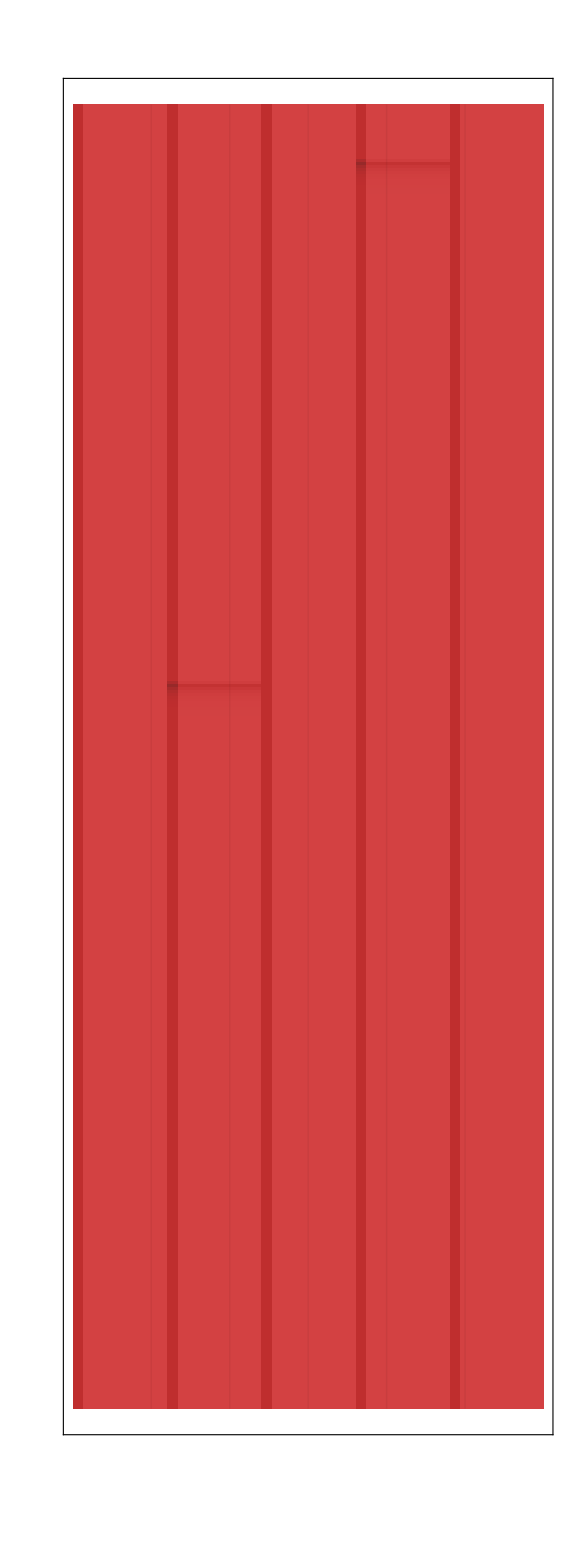
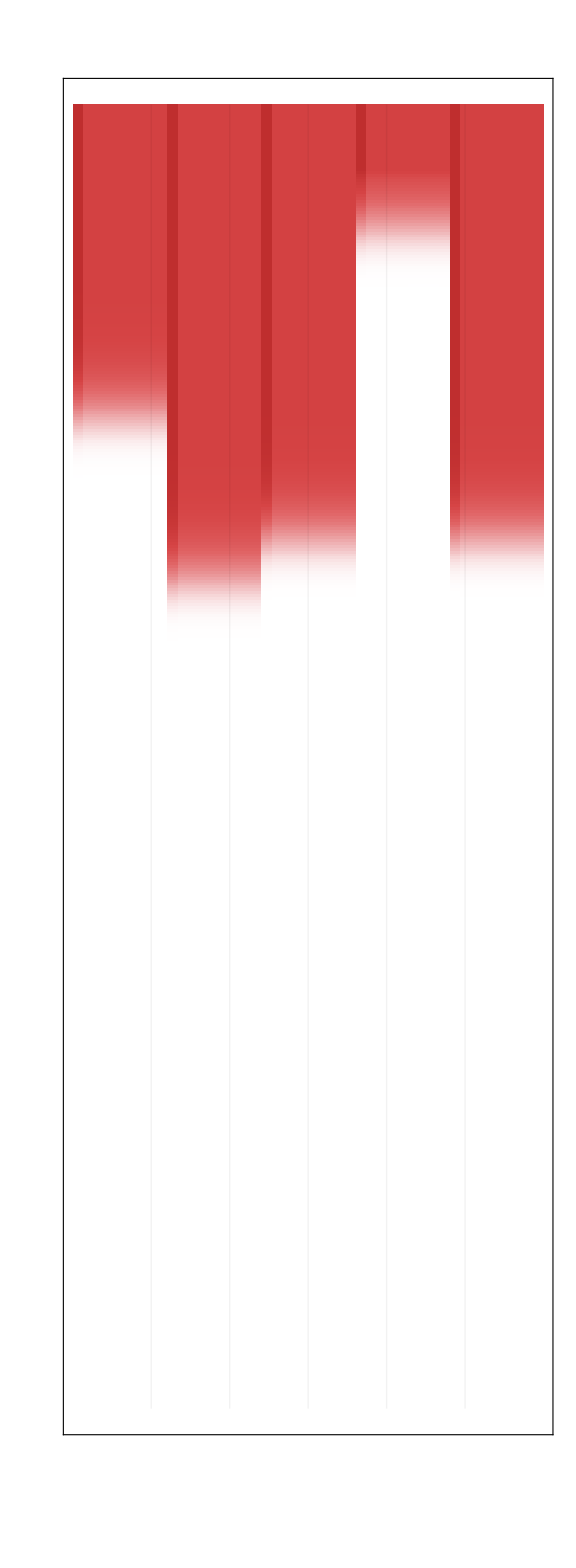
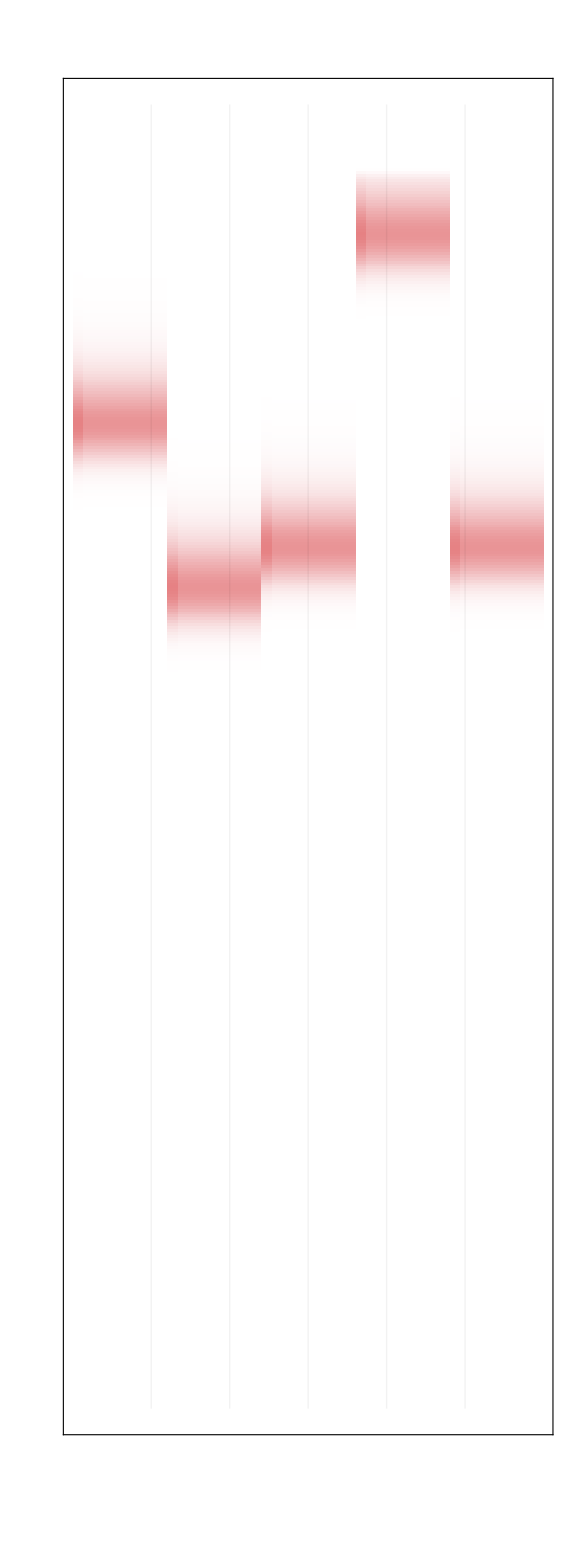
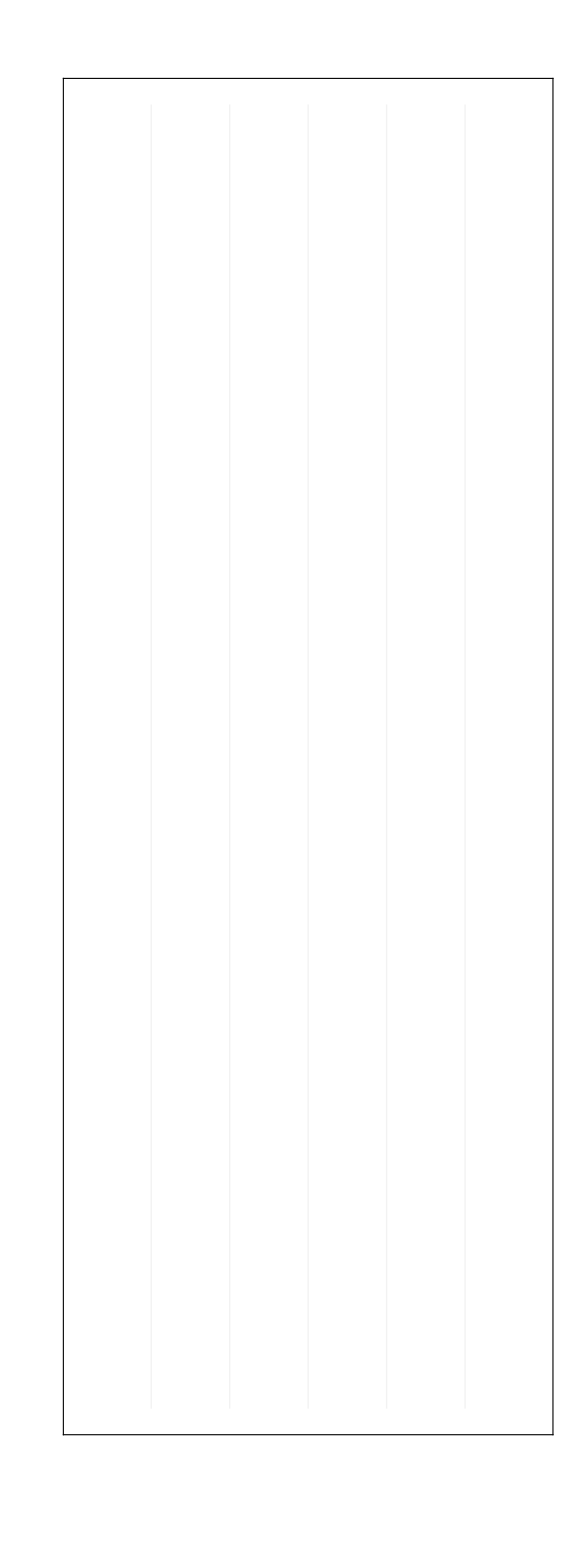
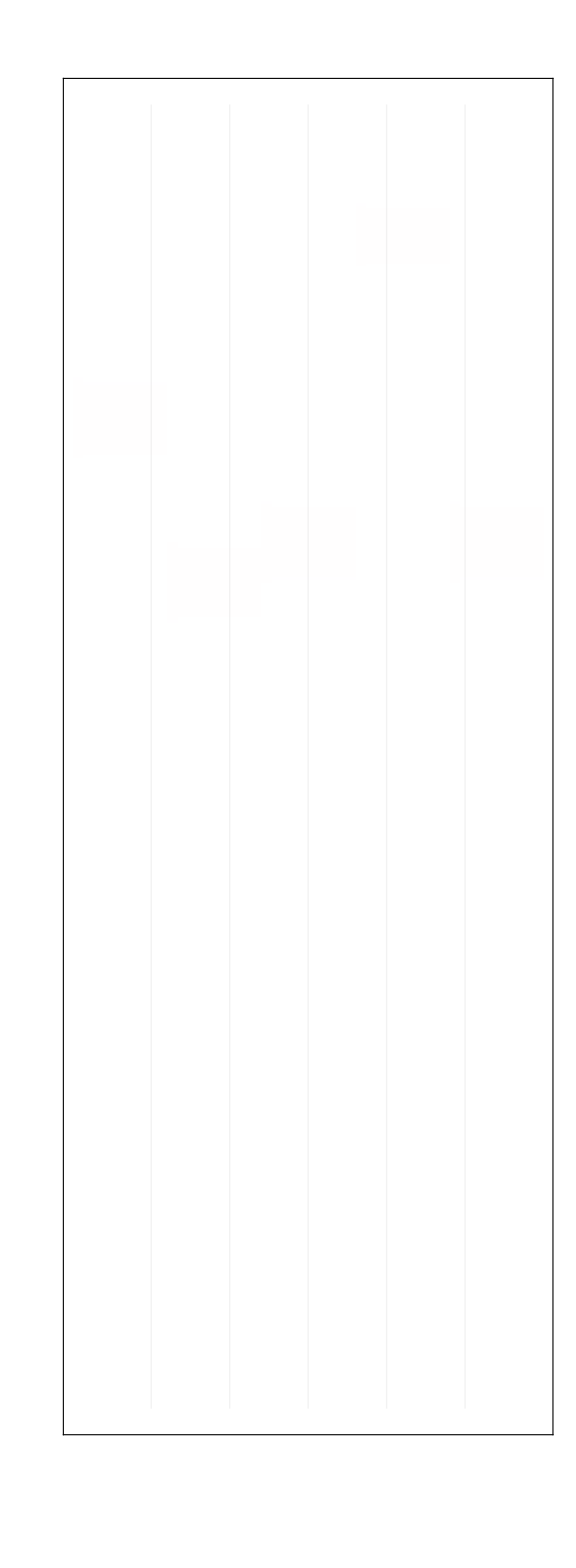
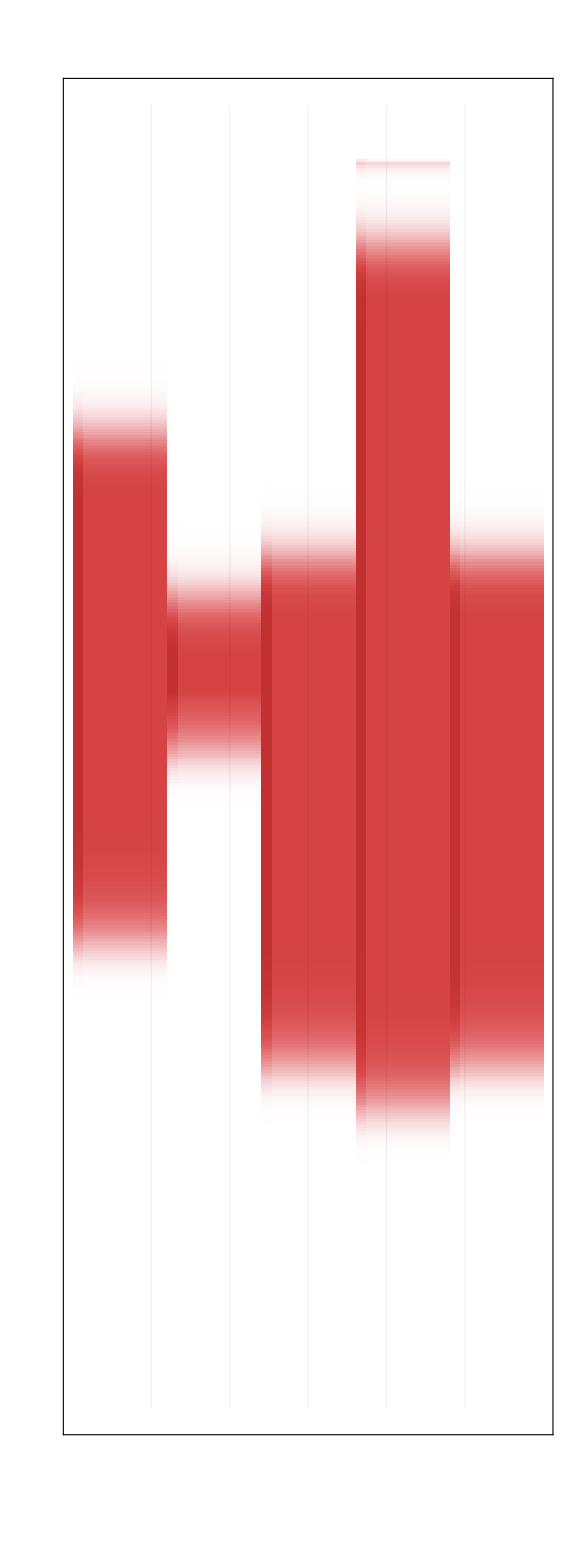
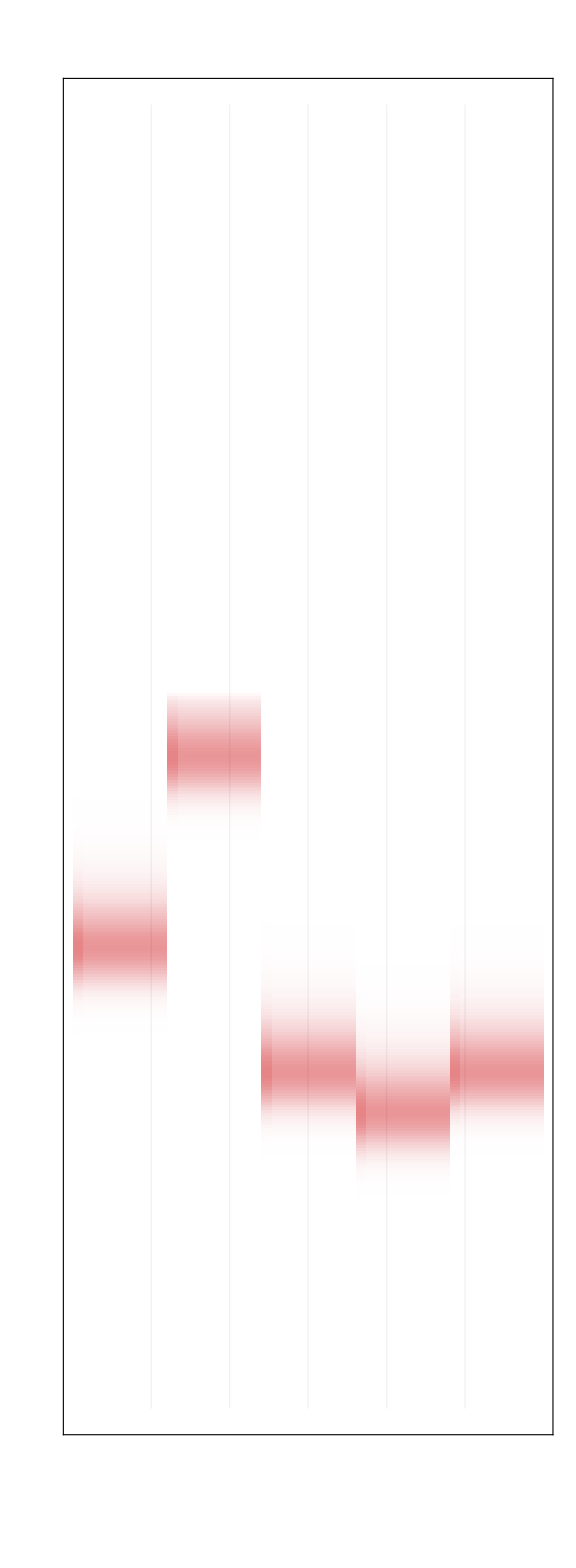
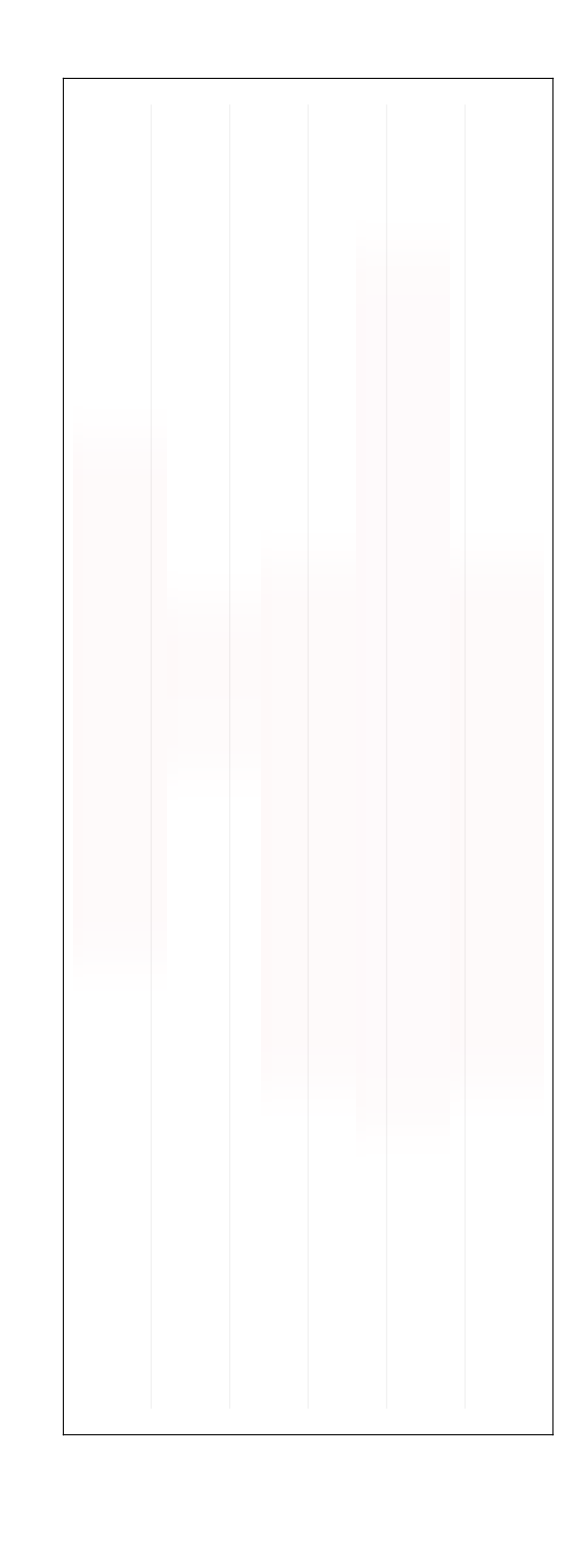
Time |  | Nodes |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Total | WW | WH | WE | WR | WB | HH | HE | HR | HB | EE | ER | EB | RR | RB | BB
 |  | 
 |  | Genotypes

NetworksDeterministicBreakdown.pdf

```mathematica
{repetition}={1};
{male,female}={1,2};
breakdowns=Table[
totalPopulation=nodesData[[repetition,male,i]]+nodesData[[repetition,female,i]]
,{i,1,nodesData[[1,1]]//Length}];
genotypesPlots=Table[
MatrixPlot[Transpose[breakdowns][[All,All,i]]
,ImageSize->Large
,AspectRatio->7.5
,Frame->True
,ImageSize->5000
,FrameTicks->None
,PlotRangePadding->None
,Mesh->{0,5}
,MeshStyle->Directive[Opacity[.05]]
,ColorFunction->ColorData[{"CherryTones",{1*breakdowns//Flatten//Max,0}}]
,ColorFunctionScaling->False
]
,{i,1,breakdowns[[1,1]]//Length}];
grid=Grid[
{
ReplacePart[ConstantArray["",genotypes//Length],1->Style ["Nodes",15]],
genotypesPlots,
Style[Rotate[#,0Degree],30]&/@genotypes
},Spacings->{0,0}]//Grid[{{Style[Rotate["Time",90Degree],50],"",#},{"","",""},{"","",Style["Genotypes",50]}}]&
Export["NetworksDeterministicBreakdown.pdf",grid,ImageSize->5000]
```

## Multi Node Stochastic (Quantile over Repetitions)

Load Data

```mathematica
(*Load data*)
baseFolder="OUT_ERACR_CPP/ImmunizingCorners";
folder=FileNames["*",baseFolder]//DeleteCases[#,baseFolder<>"/.DS_Store"]&;
dataTotal=Table[
{genotypes,dataTemp}=ImportAndReshapeData[folder[[i]]];
dataTemp
,{i,1,Length[folder]}];
{colorPalette,colorSwatch}=CreateColorSwatch[genotypes,97,{20,15}];
(*Reshape data and calculate desired quantile*)
quantile=1/2;
reshapedData={reshapedDataMale,reshapedDataFemale}=ReshapeStochasticMultiNode[dataTotal,1/2];
reshapedDataTotal=reshapedDataMale+reshapedDataFemale;
```

Explore a Single Node

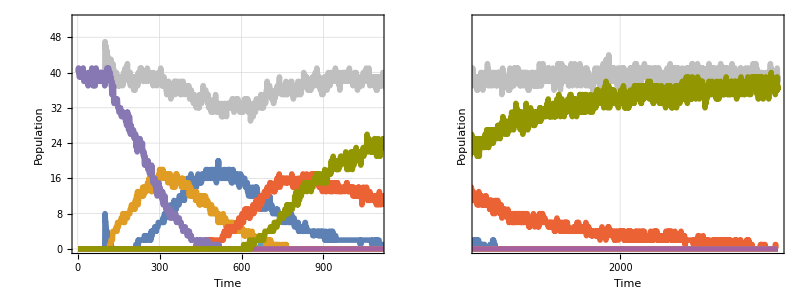
-Graphics- |  |  |  |

testNodeStochastic.pdf

```mathematica
{repetition,node}={1,44};
totalPopulation=reshapedDataMale[[node]]+reshapedDataFemale[[node]];
(*Plot results*)
plot=SplitPlotDynamics[totalPopulation,{{1,1100},{1100,3000}},colorPalette];
grid=Grid[{{plot,"","","",colorSwatch}}]
Export["testNodeStochastic.pdf",grid]
```

Explore the Network

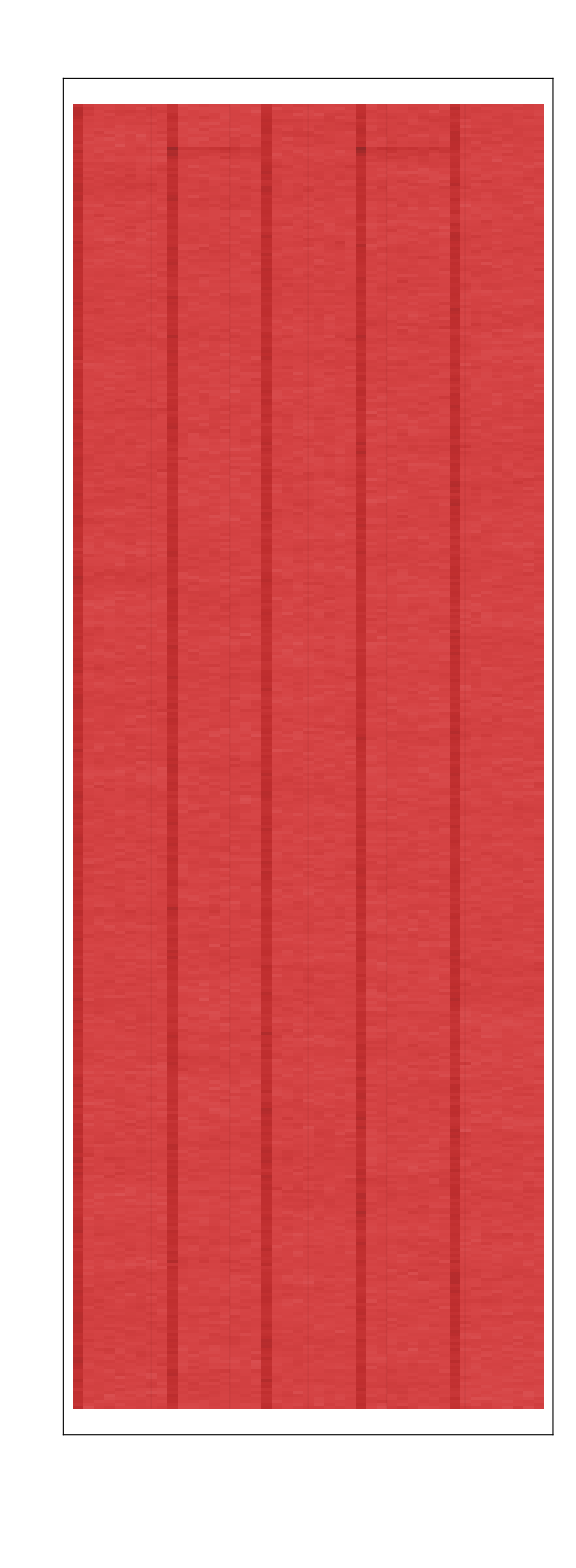
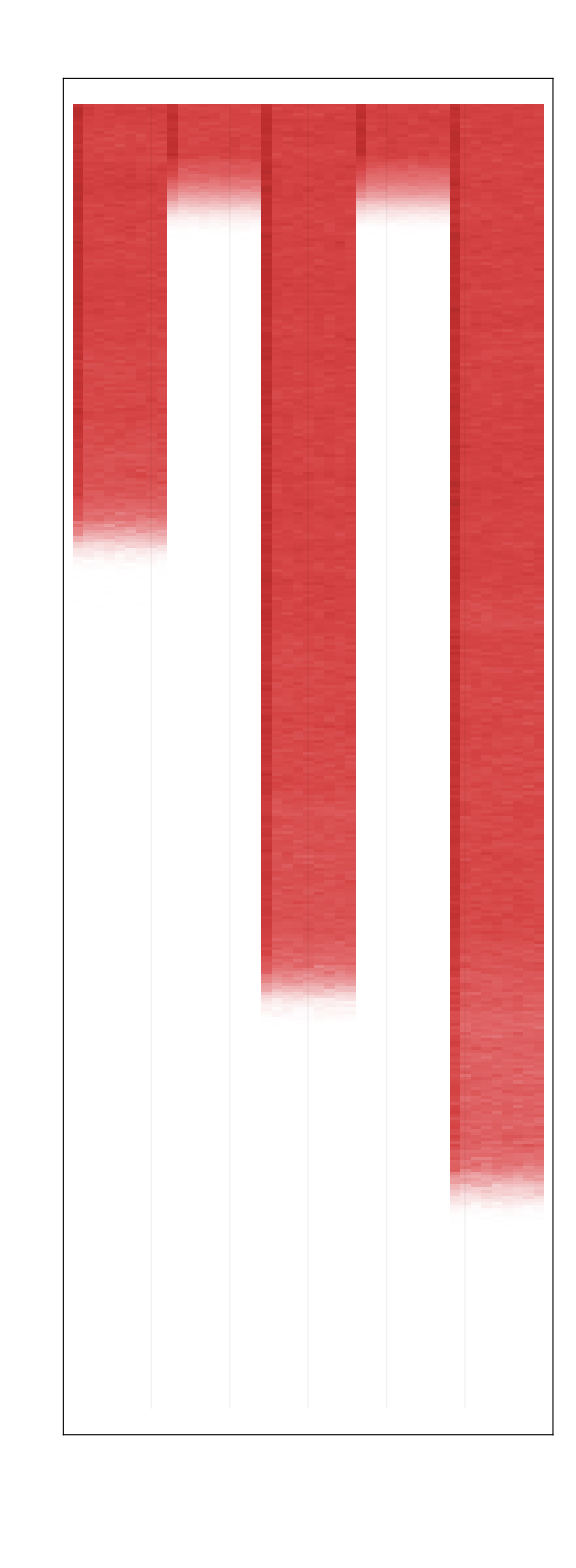
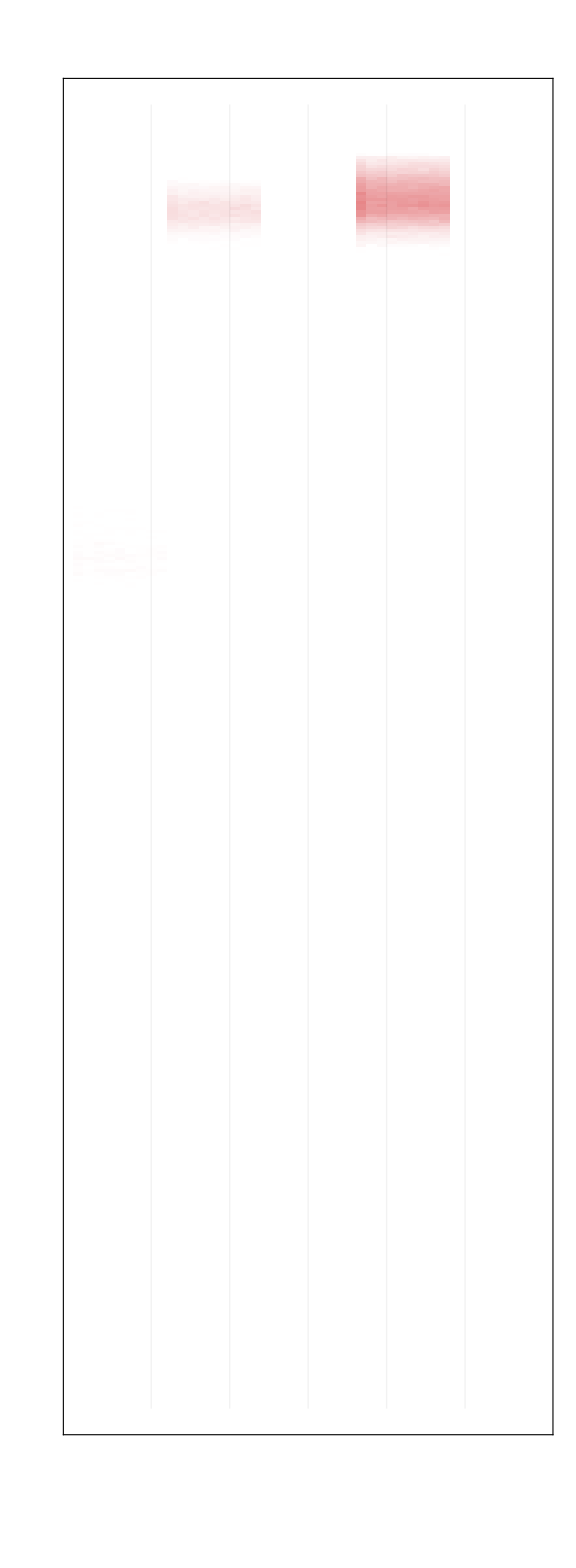
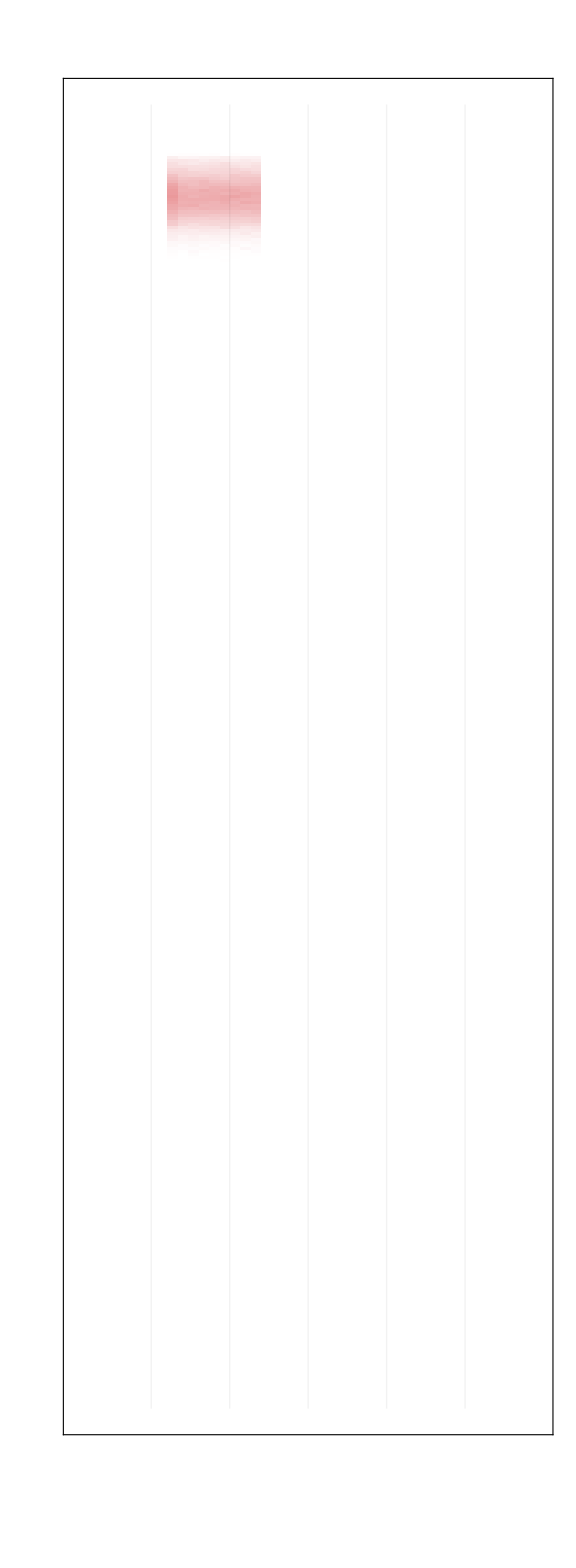
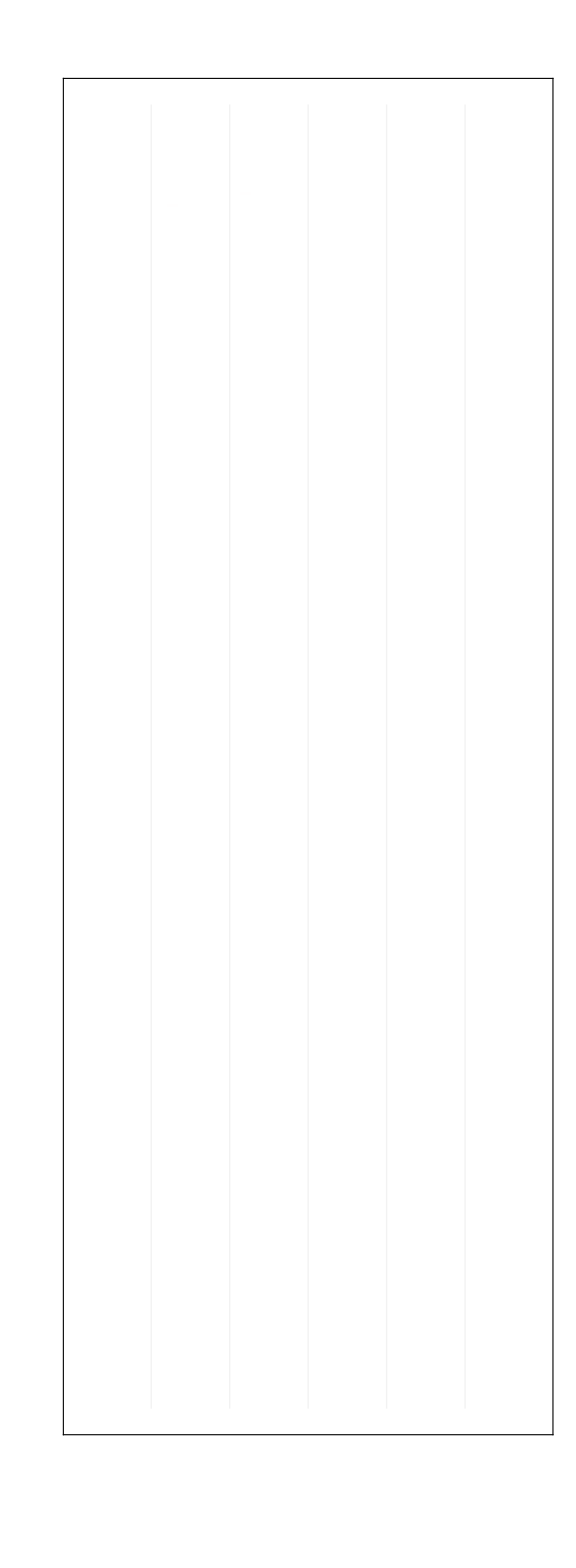
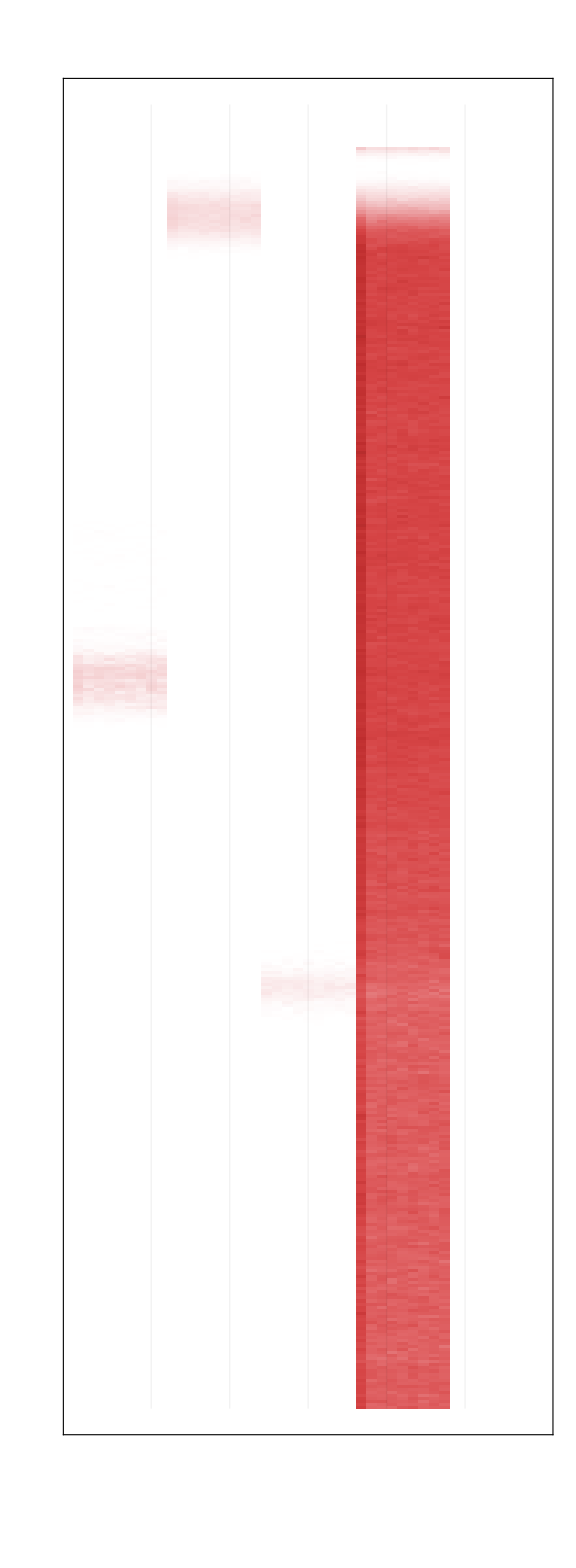
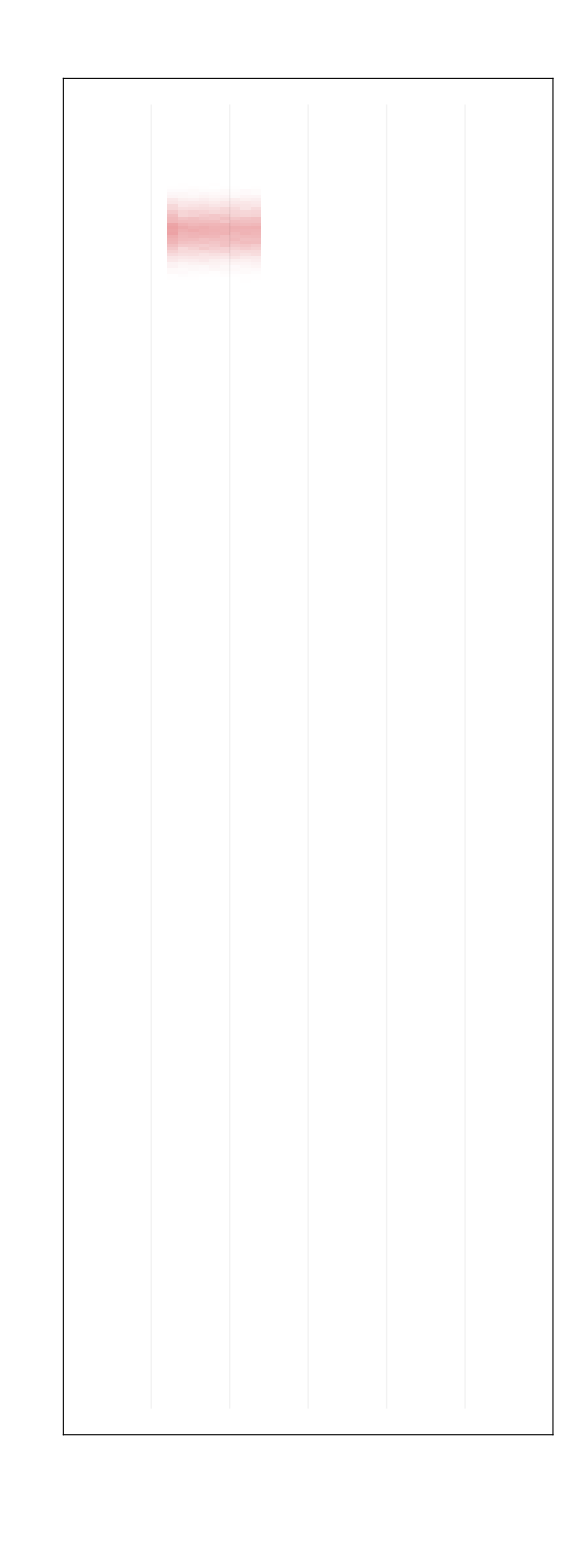
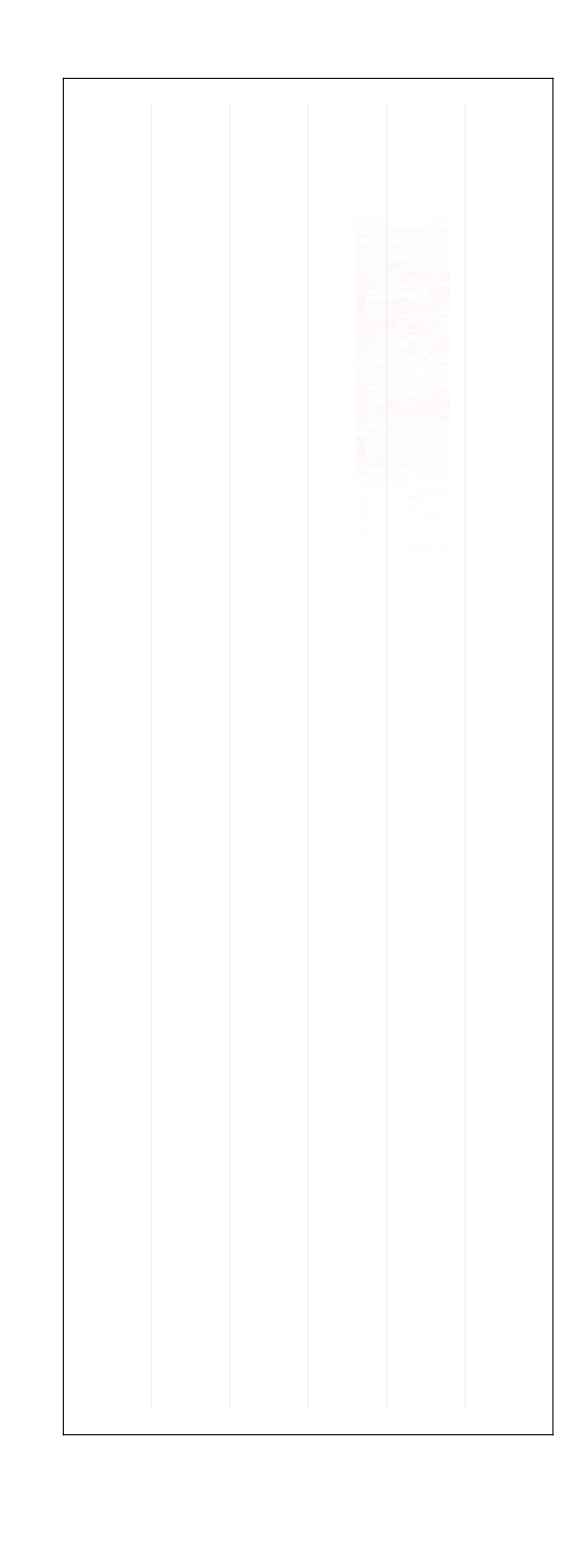
Time |  | Nodes |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Total | WW | WH | WE | WR | WB | HH | HE | HR | HB | EE | ER | EB | RR | RB | BB
 |  | 
 |  | Genotypes

NetworksStochasticBreakdown.pdf

```mathematica
genotypesPlots=Table[
MatrixPlot[Transpose[reshapedDataTotal][[All,All,i]]
,ImageSize->Large
,AspectRatio->7.5
,Frame->True
,ImageSize->5000
,FrameTicks->None
,PlotRangePadding->None
,Mesh->{0,5}
,MeshStyle->Directive[Opacity[.05]]
,ColorFunction->ColorData[{"CherryTones",{1*reshapedDataTotal//Flatten//Max,0}}]
,ColorFunctionScaling->False
]
,{i,1,reshapedDataTotal[[1,1]]//Length}];
grid=Grid[
{
ReplacePart[ConstantArray["",genotypes//Length],1->Style ["Nodes",15]],
genotypesPlots,
Style[Rotate[#,0Degree],30]&/@genotypes
},Spacings->{0,0}]//Grid[{{Style[Rotate["Time",90Degree],50],"",#},{"","",""},{"","",Style["Genotypes",50]}}]&
Export["NetworksStochasticBreakdown.pdf",grid,ImageSize->5000]
```

## Map

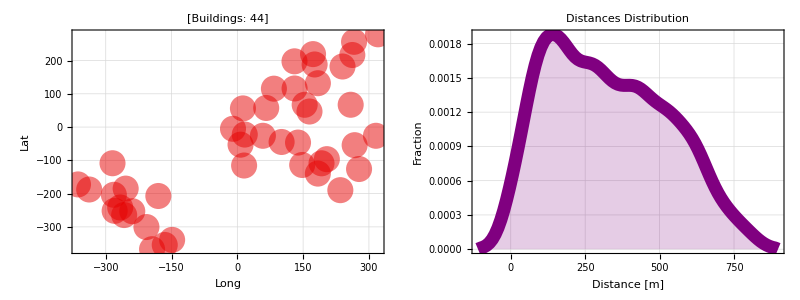

```mathematica
rawData=Map[ToExpression,Import["geoCoordinates.csv"],Infinity];
{id,geoCoordinates,sizes}={rawData[[All,1]],rawData[[All,2;;3]],rawData[[All,4]]};
coords=rawData[[All,{3,2}]];
dataOriginal=rawData[[All,{3,2}]];
buildingsPlot=ListPlot[dataOriginal,
AspectRatio->1,
GridLines->Automatic,
BaseStyle->Directive["Gray",25],
Frame->True,
FrameTicksStyle->15,
FrameStyle->Thick,
FrameLabel->{"Long","Lat"},
PlotStyle->{Darker[Red,.1],PointSize[.025],Opacity[.5]},
ImageSize->750,
PlotLabel->Style[("[Buildings: "<>ToString [dataOriginal//Length]<>"]"),25]
];
geoDistances=CalculateEuclideanDistances[sampledCoordinates];
distancesDistribution=SmoothHistogram[Flatten[geoDistances],
GridLines->Automatic,
Frame->True,
BaseStyle->Directive["Gray",25],
AspectRatio->1,
FrameStyle->Thick,
PerformanceGoal->"Speed",
FrameTicksStyle->15,
PlotStyle->Directive[Purple,Thickness[.0125]],
PlotLabel->"Distances Distribution",
ImageSize->750,
Filling->Bottom,
FrameLabel->{"Distance [m]","Fraction"}
];
originalGrid=Grid[{{buildingsPlot,distancesDistribution}}]
```